## Load the package

```mathematica
<<TRQS`
```

Package TRQS version 0.2.0 (last modification: 07/05/2012).

INFO: Using QRNG (https://qrng.physik.hu-berlin.de/) as a source of randomness.

Note: You have to use QRNGSetCredentials function to provide login information required to use this backend.

## Setup used backend (QRNG)

```mathematica
?QRNGSetCredentials
```

QRNGSetCredentials[user, pass] sets the username and the password used for connecting with the QRNG service (https://qrng.physik.hu-berlin.de/). This function must be used prior of using any functionality of the QRNG backend.

```mathematica
QRNGSetCredentials["???????","???????"] (* provide the login information for the QRNG service *)
```

User name and password for using QRNG service set!

## Check the connection

```mathematica
QRNGTestConnection[]
```

QRNG_SUCCESS

## Integer numbers

```mathematica
?TrueRandomInteger
```

TrueRandomInteger[{i_min,i_max}] returns a random integer in the range [i_min,i_max].
TrueRandomInteger[{i_min, i_max}, dim] returns a list of random integers in the range [i_min, i_max] with dim elements.
TrueRandomInteger[i] returns a random integer in the range [0,i].
TrueRandomInteger[] returns 0 or 1.

```mathematica
{TrueRandomInteger[],TrueRandomInteger[10],TrueRandomInteger[{10,20}], TrueRandomInteger[{10,20},10]}
```

{1,9,14,{11,18,16,20,10,12,19,13,18,13}}

## Real numbers

```mathematica
?TrueRandomReal
```

TrueRandomReal[{x_min,x_max}] returns a random double in the range [x_min,x_max].
TrueRandomReal[{x_min,x_max}, dim] returns a list of random double in the range [x_min,x_max] with dim elements.
TrueRandomReal[i] returns a random double in the range [0,x].
TrueRandomReal[] returns a random double in the range [0,1].

```mathematica
{TrueRandomReal[],TrueRandomReal[10],TrueRandomReal[{10,20}],TrueRandomReal[{10,20},10]}
```

{0.521969,0.281924,12.8571,{10.7352,17.2089,12.1848,12.173,13.4549,13.3945,17.9067,16.5116,17.8488,14.0846}}

## Normal distribution

```mathematica
?TrueRandomRealNormal
```

TrueRandomRealNormal[m,s,dims] provides a sample of random numbers distributed according to the normal distribution N[m,s] in an array of dimensions given by dims.

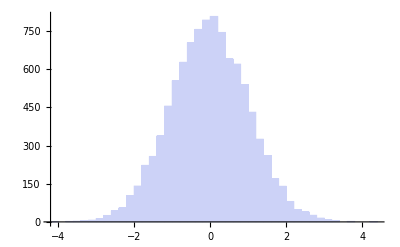

```mathematica
Histogram[Flatten[TrueRandomRealNormal[0,1,{10000}]]]
```

## Ginibre matrix

```mathematica
?TrueGinibreMatrix
```

TrueGinibreMatrix[m,n] returns (m x n)-dimensional complex matrix with entries having real and complex parts distributed according to the normal distribution N[0,1].

```mathematica
TrueGinibreMatrix[10,10]
```

{{-0.108339-0.62944 ⅈ,1.16558-0.633179 ⅈ,0.752589-0.911826 ⅈ,-2.07407+0.936491 ⅈ,-0.818169+0.59543 ⅈ,-0.881926+0.05974 ⅈ,-1.48243+1.84713 ⅈ,-0.951063-2.56268 ⅈ,-1.61383-0.865181 ⅈ,1.26992-1.06909 ⅈ},{-1.30741-0.911423 ⅈ,-1.91556+1.06268 ⅈ,0.37515-0.127827 ⅈ,0.511341+0.547687 ⅈ,-0.167391+0.809303 ⅈ,0.404585-0.547507 ⅈ,-2.339+0.657402 ⅈ,-0.778838-0.834861 ⅈ,0.319481+0.802971 ⅈ,0.139649-0.746253 ⅈ},{1.11268+0.213346 ⅈ,0.149998+0.549179 ⅈ,-1.45482-0.4898 ⅈ,-0.0129384+0.434995 ⅈ,-0.897747-0.305665 ⅈ,1.16061+0.0539393 ⅈ,0.186761+0.526669 ⅈ,0.738852+0.0763096 ⅈ,1.22265-0.727512 ⅈ,0.635233+0.474226 ⅈ},{-0.799026+0.653206 ⅈ,-0.910985-0.597074 ⅈ,0.634947-0.259534 ⅈ,-0.757998+1.69642 ⅈ,0.428439-0.881328 ⅈ,2.09653+0.642864 ⅈ,-0.277225-1.44622 ⅈ,-0.0469843-0.292951 ⅈ,1.02819-0.200624 ⅈ,1.37457+0.958766 ⅈ},{0.0742415-0.96098 ⅈ,0.918261-0.247496 ⅈ,0.226375+0.25685 ⅈ,0.737308+0.712541 ⅈ,0.41946-0.577224 ⅈ,-0.394517-0.907712 ⅈ,-2.39219+0.400287 ⅈ,-0.863331+1.32232 ⅈ,1.37059-0.839833 ⅈ,-1.84781-2.07043 ⅈ},{0.915942+0.414005 ⅈ,-0.578154-0.32092 ⅈ,-0.372269-0.0768196 ⅈ,-0.0983948+2.6749 ⅈ,-1.17693-0.495238 ⅈ,-0.414395-0.432896 ⅈ,-0.968686+1.99844 ⅈ,0.0333396-0.323216 ⅈ,1.02802-0.386716 ⅈ,-1.24038-0.14908 ⅈ},{0.359261+0.917959 ⅈ,-0.721607-0.899428 ⅈ,-1.57404-1.27354 ⅈ,-0.720017+0.526107 ⅈ,0.145106-0.0104796 ⅈ,-0.613117+0.256687 ⅈ,-1.00032-0.491414 ⅈ,0.821069-1.0153 ⅈ,0.392274-0.556593 ⅈ,-0.213135+2.96067 ⅈ},{0.85809+0.668598 ⅈ,-1.85673+1.05864 ⅈ,1.58616-1.03108 ⅈ,1.48335-2.53371 ⅈ,-0.108008-0.401638 ⅈ,-0.794431-1.53294 ⅈ,1.72969+0.704314 ⅈ,1.48574-1.34581 ⅈ,-0.111453+0.52469 ⅈ,0.924017+0.645622 ⅈ},{-0.185249+0.18713 ⅈ,-0.534222-1.09627 ⅈ,-2.62616+1.76756 ⅈ,-0.0029081-1.18939 ⅈ,1.01302+0.109831 ⅈ,1.70402-0.162919 ⅈ,-0.0343226+0.984399 ⅈ,0.522412-0.343327 ⅈ,-1.36396+0.723512 ⅈ,0.678639+1.43003 ⅈ},{-1.66916-1.73476 ⅈ,-0.637415+1.14876 ⅈ,0.27269+1.60699 ⅈ,0.783656-1.14593 ⅈ,-0.521806+0.391238 ⅈ,-1.86058-0.830168 ⅈ,2.15692+0.848221 ⅈ,0.819931-1.5721 ⅈ,1.10676+1.16252 ⅈ,0.681361+0.305842 ⅈ}}

## Random states - HS measure

```mathematica
statesHS=Table[TrueRandomStateHS[4],{2000}];
```

```mathematica
sortedEvalsHS=Map[Sort[#]&,Map[Chop[Eigenvalues[#]]&,statesHS]]ᵀ;
```

```mathematica
masterplotHS=Histogram[{sortedEvalsHS[[1]],sortedEvalsHS[[2]],sortedEvalsHS[[3]],sortedEvalsHS[[4]]},{0.005},"ProbabilityDensity",PlotRange->{{0,1},{0,61}},ChartBaseStyle->EdgeForm[None],ChartStyle->{Gray,Darker[Gray],LightGray,Darker[LightGray]},
AxesLabel->{"λ","P(λ)"},ImageSize->Large,LabelStyle-> 15];
```

```mathematica
SetDirectory[ToString[NotebookDirectory[]]<>"/plots"];
```

```mathematica
Export["lambda-prob-hs-trqs.pdf",masterplotHS];
Run[" pdf2ps  -dLanguageLevel=3 lambda-prob-hs-trqs.pdf lambda-prob-hs-trqs.eps"];
```

## Random states - Bures measure

```mathematica
statesBures=Table[TrueRandomStateBures[4],{1000}];
```

```mathematica
sortedEvalsBures=Map[Sort[#]&,Map[Chop[Eigenvalues[#]]&,statesBures]]ᵀ;
```

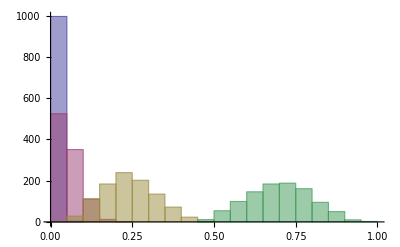

```mathematica
Histogram[{sortedEvalsBures[[1]],sortedEvalsBures[[2]],sortedEvalsBures[[3]],sortedEvalsBures[[4]]}]
```

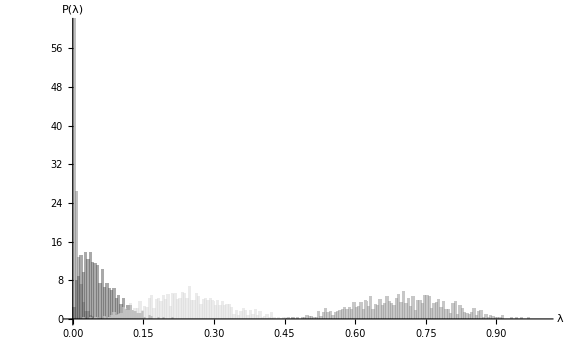

```mathematica
masterplotBures=Histogram[{sortedEvalsBures[[1]],sortedEvalsBures[[2]],sortedEvalsBures[[3]],sortedEvalsBures[[4]]},{0.005},"ProbabilityDensity",PlotRange->{{0,1},{0,61}},ChartBaseStyle->EdgeForm[None],ChartStyle->{Gray,Darker[Gray],LightGray,Darker[LightGray]},
AxesLabel->{"λ","P(λ)"},ImageSize->Large,LabelStyle-> 15]
```

```mathematica
SetDirectory[ToString[NotebookDirectory[]]<>"/plots"];
```

```mathematica
Export["lambda-prob-bures-trqs.pdf",masterplotBures];
Run[" pdf2ps  -dLanguageLevel=3 lambda-prob-bures-trqs.pdf lambda-prob-bures-trqs.eps"];
```

## libQuantis configuration

```mathematica
QuantisGetLibVersion[]
```

2.5

```mathematica
QuantisGetSerialNumber[]
```

080259A410